## From Input to Graph to visualize Petri Net.

```mathematica
systemTransitions={ {{{"H2",2},{"O2",1}}-> <|"Combine"->rate|>-> {{"H2O",2}}},
{{{"H2O",2}}-> <|"Hydrolysis"->rate2|>-> {{"H2",2},{"O2",1}}}}
```

{{{{H2,2},{O2,1}}→<|Combine→rate|>→{{H2O,2}}},{{{H2O,2}}→<|Hydrolysis→rate2|>→{{H2,2},{O2,1}}}}

```mathematica
systemInitials =<|"H2"->a1,"O2"->b1,"H2O"->c1|>
```

<|H2→a1,O2→b1,H2O→c1|>

```mathematica
pCapacities = KeyMap[p,systemInitials]
```

<|p[H2]→a1,p[O2]→b1,p[H2O]→c1|>

```mathematica
tCapacities = Join[KeyMap[t,Keys@@Values@First@systemTransitions],KeyMap[t,Keys@@Values@Last@systemTransitions]]
```

<|t[Combine]→rate,t[Hydrolysis]→rate2|>

```mathematica
initialValue[x_]:=Lookup[systemInitials,x,0]
```

```mathematica
initialValue["H2"]
```

a1

```mathematica
makeEdges[{sourcePlaces_-> transition_-> sinkPlaces_}]:= Module[{sourceEdges,sinkEdges} ,sourceEdges=DirectedEdge[p[First@#],t[First@Keys@transition]]->Last@#&/@sourcePlaces;sinkEdges=DirectedEdge[t[First@Keys@transition],p[First@#]]->Last@#&/@sinkPlaces;
Join[sourceEdges,sinkEdges]
]
```

```mathematica
edgeData= Join@@makeEdges/@systemTransitions
```

{p[H2]->t[Combine]→2,p[O2]->t[Combine]→1,t[Combine]->p[H2O]→2,p[H2O]->t[Hydrolysis]→2,t[Hydrolysis]->p[H2]→2,t[Hydrolysis]->p[O2]→1}

```mathematica
{edgeList,edgeWeights}={Keys@edgeData,Values@edgeData}
```

{{p[H2]->t[Combine],p[O2]->t[Combine],t[Combine]->p[H2O],p[H2O]->t[Hydrolysis],t[Hydrolysis]->p[H2],t[Hydrolysis]->p[O2]},{2,1,2,2,2,1}}

```mathematica
ClearAll[vsf];
vsf[scale_][pos_,p[v_],size_]:= {Circle[pos,scale First@size],Inset[v,pos]}
vsf[scale_][pos_,t[v_],size_]:= {{Transparent,Rectangle[pos- scale size,pos+scale size]},Inset[v,pos]}
```

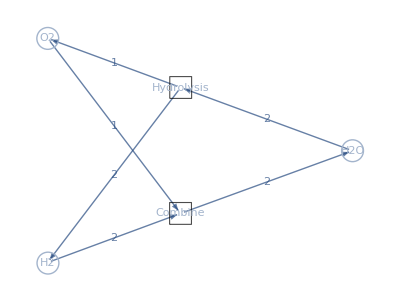

```mathematica
pNet = Graph[edgeList,VertexShapeFunction-> vsf[3],EdgeWeight->edgeWeights,EdgeLabels->"EdgeWeight"]
```

## Dynamic Analysis Using State values in Petri Net.